```mathematica
Needs["Quantum`Notation`"];
Clear[Ppτ,Pmτ,Pzτ,Pp,Pm,Pz,Q];
SetQuantumObject[Ppτ,Pmτ,Pzτ,Pp,Pm,Pz,Q];

⟦Pp,Pm⟧_-=Pz; ⟦Pz,Pp⟧_-= 2 Pp; ⟦Pz,Pm⟧_-=-2Pm;
Pp·Pz=-Pp; Pm·Pz=Pm; 
Pz·Pp=Pp; Pz·Pm=-Pm; 
Pp·Pm=1/2(1+Pz);Pm·Pp=1/2(1-Pz);
```

```mathematica
Needs["Quantum`Notation`"];
Clear[Sp,Sm,Sz,Rp,Rm,Rz,Pp,Pm,Pz,Q];
SetQuantumObject[Sp,Sm,Sz,Rp,Rm,Rz,Pp,Pm,Pz,Q];

⟦Pp,Pm⟧_-=Pz; ⟦Pz,Pp⟧_-= 2 Pp; ⟦Pz,Pm⟧_-=-2Pm;
Pp·Pz=-Pp; Pm·Pz=Pm; 
Pz·Pp=Pp; Pz·Pm=-Pm; 
Pp·Pm=1/2(1+Pz);Pm·Pp=1/2(1-Pz);

Pp·Pp=0; Pm·Pm=0;

(Pz (1/2 δ33 Cos[2 θθ] Sin[2 θ]-1/2 ⅇ^(ⅈ t ω) δ31 Cos[θ]^2 Sin[2 θθ]+1/2 ⅇ^(-ⅈ t ω) δ32 Sin[θ]^2 Sin[2 θθ])+Pp (ⅇ^(ⅈ t ω) δ11 Cos[θ]^2 Cos[θθ]^2+ⅇ^(-ⅈ t ω) δ12 Sin[θ]^2 Sin[θθ]^2+1/2 δ13 Sin[2 θ] Sin[2 θθ])+Pm (-ⅇ^(-ⅈ t ω) δ22 Cos[θθ]^2 Sin[θ]^2-ⅇ^(ⅈ t ω) δ21 Cos[θ]^2 Sin[θθ]^2+1/2 δ23 Sin[2 θ] Sin[2 θθ]))·⟦Pz (1/2 Cos[2 θθ] Sin[2 θ]-1/2 ⅇ^(-ⅈ t ω) Cos[θ]^2 Sin[2 θθ]+1/2 ⅇ^(ⅈ t ω) Sin[θ]^2 Sin[2 θθ])+Pp (-ⅇ^(ⅈ t ω) Cos[θθ]^2 Sin[θ]^2-ⅇ^(-ⅈ t ω) Cos[θ]^2 Sin[θθ]^2+1/2 Sin[2 θ] Sin[2 θθ])+Pm (ⅇ^(-ⅈ t ω) Cos[θ]^2 Cos[θθ]^2+ⅇ^(ⅈ t ω) Sin[θ]^2 Sin[θθ]^2+1/2 Sin[2 θ] Sin[2 θθ]),Q⟧_--⟦Pz (1/2 Cos[2 θθ] Sin[2 θ]-1/2 ⅇ^(ⅈ t ω) Cos[θ]^2 Sin[2 θθ]+1/2 ⅇ^(-ⅈ t ω) Sin[θ]^2 Sin[2 θθ])+Pm (-ⅇ^(-ⅈ t ω) Cos[θθ]^2 Sin[θ]^2-ⅇ^(ⅈ t ω) Cos[θ]^2 Sin[θθ]^2+1/2 Sin[2 θ] Sin[2 θθ])+Pp (ⅇ^(ⅈ t ω) Cos[θ]^2 Cos[θθ]^2+ⅇ^(-ⅈ t ω) Sin[θ]^2 Sin[θθ]^2+1/2 Sin[2 θ] Sin[2 θθ]),Q⟧_- ·(Pz (1/2 δ33 Cos[2 θθ] Sin[2 θ]-1/2 ⅇ^(-ⅈ t ω) δ31 Cos[θ]^2 Sin[2 θθ]+1/2 ⅇ^(ⅈ t ω) δ32 Sin[θ]^2 Sin[2 θθ])+Pm (ⅇ^(-ⅈ t ω) δ11 Cos[θ]^2 Cos[θθ]^2+ⅇ^(ⅈ t ω) δ12 Sin[θ]^2 Sin[θθ]^2+1/2 δ13 Sin[2 θ] Sin[2 θθ])+Pp (-ⅇ^(ⅈ t ω) δ22 Cos[θθ]^2 Sin[θ]^2-ⅇ^(-ⅈ t ω) δ21 Cos[θ]^2 Sin[θθ]^2+1/2 δ23 Sin[2 θ] Sin[2 θθ]))//Expand
```

```mathematica
-δ11 Cos[θ]^4 Cos[θθ]^4 ⟦Pp,Q⟧_-·Pm-δ12 Sin[θ]^4 Sin[θθ]^4 ⟦Pp,Q⟧_-·Pm-1/4 δ13 Sin[2 θ]^2 Sin[2 θθ]^2 ⟦Pp,Q⟧_-·Pm-δ22 Cos[θθ]^4 Sin[θ]^4 ⟦Pm,Q⟧_-·Pp-δ21 Cos[θ]^4 Sin[θθ]^4 ⟦Pm,Q⟧_-·Pp-1/4 δ23 Sin[2 θ]^2 Sin[2 θθ]^2 ⟦Pm,Q⟧_-·Pp-1/4 δ33 Cos[2 θθ]^2 Sin[2 θ]^2 ⟦Pz,Q⟧_-·Pz-1/4 δ31 Cos[θ]^4 Sin[2 θθ]^2 ⟦Pz,Q⟧_-·Pz-1/4 δ32 Sin[θ]^4 Sin[2 θθ]^2 ⟦Pz,Q⟧_-·Pz+δ11 Cos[θ]^4 Cos[θθ]^4 Pp·⟦Pm,Q⟧_-+δ12 Sin[θ]^4 Sin[θθ]^4 Pp·⟦Pm,Q⟧_-+1/4 δ13 Sin[2 θ]^2 Sin[2 θθ]^2 Pp·⟦Pm,Q⟧_-+δ22 Cos[θθ]^4 Sin[θ]^4 Pm·⟦Pp,Q⟧_-+δ21 Cos[θ]^4 Sin[θθ]^4 Pm·⟦Pp,Q⟧_-+1/4 δ23 Sin[2 θ]^2 Sin[2 θθ]^2 Pm·⟦Pp,Q⟧_-+1/4 δ33 Cos[2 θθ]^2 Sin[2 θ]^2 Pz·⟦Pz,Q⟧_-+1/4 δ31 Cos[θ]^4 Sin[2 θθ]^2 Pz·⟦Pz,Q⟧_-+1/4 δ32 Sin[θ]^4 Sin[2 θθ]^2 Pz·⟦Pz,Q⟧_-//Simplify
```

Simplify::time: Time spent on a transformation exceeded 300. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

General::stop: Further output of Simplify :: time will be suppressed during this calculation.

1/4 (-(4 δ11 Cos[θ]^4 Cos[θθ]^4+4 δ12 Sin[θ]^4 Sin[θθ]^4+δ13 Sin[2 θ]^2 Sin[2 θθ]^2) ⟦Pp,Q⟧_-·Pm-(4 δ22 Cos[θθ]^4 Sin[θ]^4+4 δ21 Cos[θ]^4 Sin[θθ]^4+δ23 Sin[2 θ]^2 Sin[2 θθ]^2) ⟦Pm,Q⟧_-·Pp-(δ33 Cos[2 θθ]^2 Sin[2 θ]^2+(δ31 Cos[θ]^4+δ32 Sin[θ]^4) Sin[2 θθ]^2) ⟦Pz,Q⟧_-·Pz+(4 δ11 Cos[θ]^4 Cos[θθ]^4+4 δ12 Sin[θ]^4 Sin[θθ]^4+δ13 Sin[2 θ]^2 Sin[2 θθ]^2) Pp·⟦Pm,Q⟧_-+(4 δ22 Cos[θθ]^4 Sin[θ]^4+4 δ21 Cos[θ]^4 Sin[θθ]^4+δ23 Sin[2 θ]^2 Sin[2 θθ]^2) Pm·⟦Pp,Q⟧_-+(δ33 Cos[2 θθ]^2 Sin[2 θ]^2+(δ31 Cos[θ]^4+δ32 Sin[θ]^4) Sin[2 θθ]^2) Pz·⟦Pz,Q⟧_-)

```mathematica
1/4 (
(4 δ11 Cos[θ]^4 Cos[θθ]^4+4 δ12 Sin[θ]^4 Sin[θθ]^4+δ13 Sin[2 θ]^2 Sin[2 θθ]^2) Pp·⟦Pm,Q⟧_--(4 δ11 Cos[θ]^4 Cos[θθ]^4+4 δ12 Sin[θ]^4 Sin[θθ]^4+δ13 Sin[2 θ]^2 Sin[2 θθ]^2) ⟦Pp,Q⟧_-·Pm
+(4 δ22 Cos[θθ]^4 Sin[θ]^4+4 δ21 Cos[θ]^4 Sin[θθ]^4+δ23 Sin[2 θ]^2 Sin[2 θθ]^2) Pm·⟦Pp,Q⟧_--(4 δ22 Cos[θθ]^4 Sin[θ]^4+4 δ21 Cos[θ]^4 Sin[θθ]^4+δ23 Sin[2 θ]^2 Sin[2 θθ]^2) ⟦Pm,Q⟧_-·Pp
+(δ33 Cos[2 θθ]^2 Sin[2 θ]^2+(δ31 Cos[θ]^4+δ32 Sin[θ]^4) Sin[2 θθ]^2) Pz·⟦Pz,Q⟧_--(δ33 Cos[2 θθ]^2 Sin[2 θ]^2+(δ31 Cos[θ]^4+δ32 Sin[θ]^4) Sin[2 θθ]^2) ⟦Pz,Q⟧_-·Pz
)
```

```mathematica
1/4 ((4 δ11 Cos[θ]^4 Cos[θθ]^4+4 δ12 Sin[θ]^4 Sin[θθ]^4+δ13 Sin[2 θ]^2 Sin[2 θθ]^2) Pp·⟦Pm,Q⟧_--(4 δ11 Cos[θ]^4 Cos[θθ]^4+4 δ12 Sin[θ]^4 Sin[θθ]^4+δ13 Sin[2 θ]^2 Sin[2 θθ]^2) ⟦Pp,Q⟧_-·Pm)//Simplify
```

1/4 (4 δ11 Cos[θ]^4 Cos[θθ]^4+4 δ12 Sin[θ]^4 Sin[θθ]^4+δ13 Sin[2 θ]^2 Sin[2 θθ]^2) (-(⟦Pp,Q⟧_-·Pm)+Pp·⟦Pm,Q⟧_-)

```mathematica
1/4 ((4 δ22 Cos[θθ]^4 Sin[θ]^4+4 δ21 Cos[θ]^4 Sin[θθ]^4+δ23 Sin[2 θ]^2 Sin[2 θθ]^2) Pm·⟦Pp,Q⟧_--(4 δ22 Cos[θθ]^4 Sin[θ]^4+4 δ21 Cos[θ]^4 Sin[θθ]^4+δ23 Sin[2 θ]^2 Sin[2 θθ]^2) ⟦Pm,Q⟧_-·Pp)//Simplify
```

1/4 (4 δ22 Cos[θθ]^4 Sin[θ]^4+4 δ21 Cos[θ]^4 Sin[θθ]^4+δ23 Sin[2 θ]^2 Sin[2 θθ]^2) (-(⟦Pm,Q⟧_-·Pp)+Pm·⟦Pp,Q⟧_-)

```mathematica
1/4 ((δ33 Cos[2 θθ]^2 Sin[2 θ]^2+(δ31 Cos[θ]^4+δ32 Sin[θ]^4) Sin[2 θθ]^2) Pz·⟦Pz,Q⟧_--(δ33 Cos[2 θθ]^2 Sin[2 θ]^2+(δ31 Cos[θ]^4+δ32 Sin[θ]^4) Sin[2 θθ]^2) ⟦Pz,Q⟧_-·Pz)//Simplify
```

-1/4 (δ33 Cos[2 θθ]^2 Sin[2 θ]^2+(δ31 Cos[θ]^4+δ32 Sin[θ]^4) Sin[2 θθ]^2) (⟦Pz,Q⟧_-·Pz-Pz·⟦Pz,Q⟧_-)

```mathematica
1/4 (4 δ11 Cos[θ]^4 Cos[θθ]^4+4 δ12 Sin[θ]^4 Sin[θθ]^4+δ13 Sin[2 θ]^2 Sin[2 θθ]^2) (Pp·⟦Pm,Q⟧_--⟦Pp,Q⟧_-·Pm)+1/4 (4 δ22 Cos[θθ]^4 Sin[θ]^4+4 δ21 Cos[θ]^4 Sin[θθ]^4+δ23 Sin[2 θ]^2 Sin[2 θθ]^2) (Pm·⟦Pp,Q⟧_--⟦Pm,Q⟧_-·Pp)+1/4 (δ33 Cos[2 θθ]^2 Sin[2 θ]^2+(δ31 Cos[θ]^4+δ32 Sin[θ]^4) Sin[2 θθ]^2) (Pz·⟦Pz,Q⟧_--⟦Pz,Q⟧_-·Pz)
```

```mathematica
Q=Pz·Pz;
I G⟦Pz,Q⟧_--Γp (Pp·⟦Pm,Q⟧_--⟦Pp,Q⟧_-·Pm)-Γm (Pm·⟦Pp,Q⟧_--⟦Pm,Q⟧_-·Pp)-Γ0 (Pz·⟦Pz,Q⟧_--⟦Pz,Q⟧_-·Pz)//Simplify
```

0

```mathematica
Solve[{Sp==Cos[θ]^2 Rp Exp[I ω t]-Sin[θ]^2 Rm Exp[-I ω t]+1/2 Sin[2 θ] Rz, Sm==Cos[θ]^2 Rm Exp[-I ω t]-Sin[θ]^2 Rp Exp[I ω t]+1/2 Sin[2 θ] Rz, Sz==1/2 Cos[2 θ] Rz-1/2 Sin[2 θ] (Rp Exp[I ω t]+Rm Exp[-I ω t])},{Rp,Rm,Rz}]//FullSimplify
```

{{Rp→1/2 ⅇ^(-ⅈ t ω) (-Sm+Sp+(Sm+Sp) Cos[2 θ]-2 Sz Sin[2 θ]),Rm→1/2 ⅇ^(ⅈ t ω) (Sm-Sp+(Sm+Sp) Cos[2 θ]-2 Sz Sin[2 θ]),Rz→2 Sz Cos[2 θ]+(Sm+Sp) Sin[2 θ]}}

```mathematica
Solve[{
1/2 ⅇ^(-ⅈ t ω) (-Sm+Sp+(Sm+Sp) Cos[2 θ]-2 Sz Sin[2 θ])==Cos[θθ]^2 Pp-Sin[θθ]^2 Pm-1/2 Sin[2 θθ] Pz, 
1/2 ⅇ^(ⅈ t ω) (Sm-Sp+(Sm+Sp) Cos[2 θ]-2 Sz Sin[2 θ])==Cos[θθ]^2 Pm-Sin[θθ]^2 Pp-1/2 Sin[2 θθ] Pz, 
2 Sz Cos[2 θ]+(Sm+Sp) Sin[2 θ]==Cos[2 θθ] Pz+Sin[2 θθ] (Pp+Pm)},{Sp,Sm,Sz}]//FullSimplify
```

{{Sp→ⅇ^(ⅈ t ω) Cos[θ]^2 (Pp Cos[θθ]^2-Pz Cos[θθ] Sin[θθ]-Pm Sin[θθ]^2)+ⅇ^(-ⅈ t ω) Sin[θ]^2 (-Pm Cos[θθ]^2+Pz Cos[θθ] Sin[θθ]+Pp Sin[θθ]^2)+1/2 Sin[2 θ] (Pz Cos[2 θθ]+(Pm+Pp) Sin[2 θθ]),Sm→1/2 ⅇ^(-ⅈ t ω) (ⅇ^(ⅈ t ω) Sin[2 θ] (Pz Cos[2 θθ]+(Pm+Pp) Sin[2 θθ])+Cos[θ]^2 (Pm-Pp+(Pm+Pp) Cos[2 θθ]-Pz Sin[2 θθ])-ⅇ^(2 ⅈ t ω) Sin[θ]^2 (-Pm+Pp+(Pm+Pp) Cos[2 θθ]-Pz Sin[2 θθ])),Sz→1/4 ⅇ^(-ⅈ t ω) (2 ⅇ^(ⅈ t ω) Cos[2 θ] (Pz Cos[2 θθ]+(Pm+Pp) Sin[2 θθ])+Sin[2 θ] (-Pm+Pp-(1+ⅇ^(2 ⅈ t ω)) (Pm+Pp) Cos[2 θθ]+Pz Sin[2 θθ]+ⅇ^(2 ⅈ t ω) (Pm-Pp+Pz Sin[2 θθ])))}}

```mathematica
Sp=ⅇ^(ⅈ t ω) Cos[θ]^2 (Pp Cos[θθ]^2-Pz Cos[θθ] Sin[θθ]-Pm Sin[θθ]^2)+ⅇ^(-ⅈ t ω) Sin[θ]^2 (-Pm Cos[θθ]^2+Pz Cos[θθ] Sin[θθ]+Pp Sin[θθ]^2)+1/2 Sin[2 θ] (Pz Cos[2 θθ]+(Pm+Pp) Sin[2 θθ]);
Sm=1/2 ⅇ^(-ⅈ t ω) (ⅇ^(ⅈ t ω) Sin[2 θ] (Pz Cos[2 θθ]+(Pm+Pp) Sin[2 θθ])+Cos[θ]^2 (Pm-Pp+(Pm+Pp) Cos[2 θθ]-Pz Sin[2 θθ])-ⅇ^(2 ⅈ t ω) Sin[θ]^2 (-Pm+Pp+(Pm+Pp) Cos[2 θθ]-Pz Sin[2 θθ]));
Sz=1/4 ⅇ^(-ⅈ t ω) (2 ⅇ^(ⅈ t ω) Cos[2 θ] (Pz Cos[2 θθ]+(Pm+Pp) Sin[2 θθ])+Sin[2 θ] (-Pm+Pp-(1+ⅇ^(2 ⅈ t ω)) (Pm+Pp) Cos[2 θθ]+Pz Sin[2 θθ]+ⅇ^(2 ⅈ t ω) (Pm-Pp+Pz Sin[2 θθ])))//FullSimplify
```

1/4 ⅇ^(-ⅈ t ω) (2 ⅇ^(ⅈ t ω) Cos[2 θ] (Pz Cos[2 θθ]+(Pm+Pp) Sin[2 θθ])+Sin[2 θ] (-Pm+Pp-(1+ⅇ^(2 ⅈ t ω)) (Pm+Pp) Cos[2 θθ]+Pz Sin[2 θθ]+ⅇ^(2 ⅈ t ω) (Pm-Pp+Pz Sin[2 θθ])))

```mathematica
Sp=ⅇ^(ⅈ t ω) Cos[θ]^2 (Pp Cos[θθ]^2-Pz 1/2 Sin[2 θθ]-Pm Sin[θθ]^2)+ⅇ^(-ⅈ t ω) Sin[θ]^2 (-Pm Cos[θθ]^2+Pz 1/2 Sin[2 θθ]+Pp Sin[θθ]^2)+1/2 Sin[2 θ] (Pz Cos[2 θθ]+(Pm+Pp) Sin[2 θθ]);
Spτ=ⅇ^(ⅈ (t+τ) ω) Cos[θ]^2 (Ppτ Cos[θθ]^2-Pzτ 1/2 Sin[2 θθ]-Pmτ Sin[θθ]^2)+ⅇ^(-ⅈ (t+τ) ω) Sin[θ]^2 (-Pmτ Cos[θθ]^2+Pzτ 1/2 Sin[2 θθ]+Ppτ Sin[θθ]^2)+1/2 Sin[2 θ] (Pzτ Cos[2 θθ]+(Pmτ+Ppτ) Sin[2 θθ]);
Sm=ⅇ^(-ⅈ t ω) Cos[θ]^2 (Pm Cos[θθ]^2-Pz 1/2 Sin[2 θθ]-Pp Sin[θθ]^2)+ⅇ^(ⅈ t ω) Sin[θ]^2 (-Pp Cos[θθ]^2+Pz 1/2 Sin[2 θθ]+Pm Sin[θθ]^2)+1/2 Sin[2 θ] (Pz Cos[2 θθ]+(Pm+Pp) Sin[2 θθ]);
Smτ=ⅇ^(-ⅈ (t+τ) ω) Cos[θ]^2 (Pmτ Cos[θθ]^2-Pzτ 1/2 Sin[2 θθ]-Ppτ Sin[θθ]^2)+ⅇ^(ⅈ( t+τ) ω) Sin[θ]^2 (-Ppτ Cos[θθ]^2+Pzτ 1/2 Sin[2 θθ]+Pmτ Sin[θθ]^2)+1/2 Sin[2 θ] (Pzτ Cos[2 θθ]+(Pmτ+Ppτ) Sin[2 θθ]);
Sz=-Sin[2 θ] 1/4 ⅇ^(ⅈ t ω)(2 Cos[θθ]^2 Pp-2 Sin[θθ]^2 Pm-Sin[2 θθ]Pz)-Sin[2 θ] 1/4 ⅇ^(-ⅈ t ω) (2 Cos[θθ]^2 Pm-2 Sin[θθ]^2 Pp-Sin[2 θθ]Pz)+1/2 Cos[2 θ] (Pz Cos[2 θθ]+(Pm+Pp) Sin[2 θθ]);
Szτ=-Sin[2 θ] 1/4 ⅇ^(ⅈ (t+τ) ω)(2 Cos[θθ]^2 Ppτ-2 Sin[θθ]^2 Pmτ-Sin[2 θθ]Pzτ)-Sin[2 θ] 1/4 ⅇ^(-ⅈ (t+τ) ω) (2 Cos[θθ]^2 Pmτ-2 Sin[θθ]^2 Ppτ-Sin[2 θθ]Pzτ)+1/2 Cos[2 θ] (Pzτ Cos[2 θθ]+(Pmτ+Ppτ) Sin[2 θθ]);
```

```mathematica
Smτ ·Sm//Expand
```

```mathematica
(-ⅇ^(ⅈ τ ω)1/4 Sin[2 θ]^2  Cos[θθ]^4 -ⅇ^(-ⅈ τ ω) 1/4 Sin[2 θ]^2  Sin[θθ]^4  +1/4 Sin[2 θ]^2 Sin[2 θθ]^2 )Ppτ·Pm+(-ⅇ^(-ⅈ τ ω)1/4 Sin[2 θ]^2 Cos[θθ]^4   -ⅇ^(ⅈ τ ω)1/4 Sin[2 θ]^2  Sin[θθ]^4 +1/4 Sin[2 θ]^2 Sin[2 θθ]^2 )Pmτ·Pp+(1/4 Cos[2 θθ]^2 Sin[2 θ]^2  -1/16 ⅇ^(-ⅈ τ ω)  Sin[2 θ]^2  Sin[2 θθ]^2 -1/16 ⅇ^(ⅈ τ ω)  Sin[2 θ]^2  Sin[2 θθ]^2 )Pzτ·Pz
```

```mathematica
ⅇ^(-ⅈ t ω+ⅈ (t+τ) ω)//Simplify
```

ⅇ^(ⅈ τ ω)

```mathematica
SmτSm=(-ⅇ^(ⅈ τ ω)1/4 Sin[2 θ]^2  Cos[θθ]^4 -ⅇ^(-ⅈ τ ω) 1/4 Sin[2 θ]^2  Sin[θθ]^4  +1/4 Sin[2 θ]^2 Sin[2 θθ]^2 )Ppτ·Pm+(-ⅇ^(-ⅈ τ ω)1/4 Sin[2 θ]^2 Cos[θθ]^4   -ⅇ^(ⅈ τ ω)1/4 Sin[2 θ]^2  Sin[θθ]^4 +1/4 Sin[2 θ]^2 Sin[2 θθ]^2 )Pmτ·Pp+(1/4 Cos[2 θθ]^2 Sin[2 θ]^2  -1/16 ⅇ^(-ⅈ τ ω)  Sin[2 θ]^2  Sin[2 θθ]^2 -1/16 ⅇ^(ⅈ τ ω)  Sin[2 θ]^2  Sin[2 θθ]^2 )Pzτ·Pz;
SmSmτ=(-ⅇ^(-ⅈ (2 t+τ) ω) (ⅇ^(ⅈ (t+τ) ω) Cos[θθ] Sin[θ]-Cos[θ] Sin[θθ])^2 (Cos[θ] Cos[θθ]+ⅇ^(ⅈ t ω) Sin[θ] Sin[θθ])^2) Pm·Ppτ+(-1/2 ⅇ^(-ⅈ (2 t+τ) ω) (Cos[θ] Cos[θθ]+ⅇ^(ⅈ (t+τ) ω) Sin[θ] Sin[θθ])^2 (2 ⅇ^(2 ⅈ t ω) Cos[θθ]^2 Sin[θ]^2+2 Cos[θ]^2 Sin[θθ]^2-ⅇ^(ⅈ t ω) Sin[2 θ] Sin[2 θθ])) Pp·Pmτ+(1/4 ⅇ^(-ⅈ (2 t+τ) ω) (ⅇ^(ⅈ t ω) Cos[2 θθ] Sin[2 θ]-(Cos[θ]^2-ⅇ^(2 ⅈ t ω) Sin[θ]^2) Sin[2 θθ]) (ⅇ^(ⅈ (t+τ) ω) Cos[2 θθ] Sin[2 θ]-(Cos[θ]^2-ⅇ^(2 ⅈ (t+τ) ω) Sin[θ]^2) Sin[2 θθ])) Pz·Pzτ;
```

```mathematica
SpSpτ=(-1/2 ⅇ^(-ⅈ (2 t+τ) ω) (ⅇ^(ⅈ (t+τ) ω) Cos[θ] Cos[θθ]+Sin[θ] Sin[θθ])^2 (2 Cos[θθ]^2 Sin[θ]^2+2 ⅇ^(2 ⅈ t ω) Cos[θ]^2 Sin[θθ]^2-ⅇ^(ⅈ t ω) Sin[2 θ] Sin[2 θθ])) Pm·Ppτ+(-ⅇ^(-ⅈ (2 t+τ) ω) (Cos[θθ] Sin[θ]-ⅇ^(ⅈ (t+τ) ω) Cos[θ] Sin[θθ])^2 (ⅇ^(ⅈ t ω) Cos[θ] Cos[θθ]+Sin[θ] Sin[θθ])^2) Pp·Pmτ+(-1/4 ⅇ^(-ⅈ (2 t+τ) ω) (-ⅇ^(ⅈ t ω) Cos[2 θθ] Sin[2 θ]+(ⅇ^(2 ⅈ t ω) Cos[θ]^2-Sin[θ]^2) Sin[2 θθ]) (ⅇ^(ⅈ (t+τ) ω) Cos[2 θθ] Sin[2 θ]-(ⅇ^(2 ⅈ (t+τ) ω) Cos[θ]^2-Sin[θ]^2) Sin[2 θθ])) Pz·Pzτ;
```

```mathematica
SpτSm=(ⅇ^(-ⅈ (2 t+τ) ω) (ⅇ^(ⅈ (t+τ) ω) Cos[θ] Cos[θθ]+Sin[θ] Sin[θθ])^2 (Cos[θ] Cos[θθ]+ⅇ^(ⅈ t ω) Sin[θ] Sin[θθ])^2) Ppτ·Pm+(1/2 ⅇ^(-ⅈ (2 t+τ) ω) (Cos[θθ] Sin[θ]-ⅇ^(ⅈ (t+τ) ω) Cos[θ] Sin[θθ])^2 (2 ⅇ^(2 ⅈ t ω) Cos[θθ]^2 Sin[θ]^2+2 Cos[θ]^2 Sin[θθ]^2-ⅇ^(ⅈ t ω) Sin[2 θ] Sin[2 θθ])) Pmτ·Pp+(-1/4 ⅇ^(-ⅈ (2 t+τ) ω) (-ⅇ^(ⅈ (t+τ) ω) Cos[2 θθ] Sin[2 θ]+(ⅇ^(2 ⅈ (t+τ) ω) Cos[θ]^2-Sin[θ]^2) Sin[2 θθ]) (ⅇ^(ⅈ t ω) Cos[2 θθ] Sin[2 θ]-(Cos[θ]^2-ⅇ^(2 ⅈ t ω) Sin[θ]^2) Sin[2 θθ])) Pzτ·Pz;
```

```mathematica
SpSmτ=(ⅇ^(-ⅈ (2 t+τ) ω) (ⅇ^(ⅈ t ω) Cos[θ] Cos[θθ]+Sin[θ] Sin[θθ])^2 (Cos[θ] Cos[θθ]+ⅇ^(ⅈ (t+τ) ω) Sin[θ] Sin[θθ])^2) Pp·Pmτ+(1/2 ⅇ^(-ⅈ (2 t+τ) ω) (ⅇ^(ⅈ (t+τ) ω) Cos[θθ] Sin[θ]-Cos[θ] Sin[θθ])^2 (2 Cos[θθ]^2 Sin[θ]^2+2 ⅇ^(2 ⅈ t ω) Cos[θ]^2 Sin[θθ]^2-ⅇ^(ⅈ t ω) Sin[2 θ] Sin[2 θθ])) Pm·Ppτ+(-1/4 ⅇ^(-ⅈ (2 t+τ) ω) (-ⅇ^(ⅈ t ω) Cos[2 θθ] Sin[2 θ]+(ⅇ^(2 ⅈ t ω) Cos[θ]^2-Sin[θ]^2) Sin[2 θθ]) (ⅇ^(ⅈ (t+τ) ω) Cos[2 θθ] Sin[2 θ]-(Cos[θ]^2-ⅇ^(2 ⅈ (t+τ) ω) Sin[θ]^2) Sin[2 θθ])) Pz·Pzτ;
```

```mathematica
Ppτ=Pp Exp[(2I G-Γs) (τ)];
Pmτ=Pm Exp[(-2I G-Γs) (τ)];
Pzτ=ⅇ^(-2 (Γm+Γp) (τ)) Pz+Zτ(* Z=(ⅇ^(-2 (Γm+Γp) (τ)) (-Γm+ⅇ^(2 (Γm+Γp) (τ)) Γm+Γp-ⅇ^(2 (Γm+Γp) (τ)) Γp))/(Γm+Γp) *);
```

```mathematica
SmPSmτ=(1/4 Cos[2 θθ]^2 Sin[2 θ]^2-1/16 ⅇ^(-ⅈ τ ω)  Sin[2 θ]^2 Sin[2 θθ]^2-1/16 ⅇ^(ⅈ τ ω)  Sin[2 θ]^2 Sin[2 θθ]^2)Pz Pzτ ;
SpPSpτ=(1/4 Cos[2 θθ]^2 Sin[2 θ]^2-1/16 ⅇ^(-ⅈ τ ω)  Sin[2 θ]^2 Sin[2 θθ]^2-1/16 ⅇ^(ⅈ τ ω)   Sin[2 θ]^2 Sin[2 θθ]^2)Pz Pzτ;
SpτPSm=(1/4 Cos[2 θθ]^2 Sin[2 θ]^2+1/4 ⅇ^(ⅈ τ ω) Cos[θ]^4 Sin[2 θθ]^2+1/4 ⅇ^(-ⅈ τ ω)  Sin[θ]^4 Sin[2 θθ]^2)Pz Pzτ;
SpPSmτ=(1/4 Cos[2 θθ]^2 Sin[2 θ]^2+1/4 ⅇ^(-ⅈ τ ω) Cos[θ]^4 Sin[2 θθ]^2+1/4 ⅇ^(ⅈ τ ω)  Sin[θ]^4 Sin[2 θθ]^2)Pz Pzτ;
```

```mathematica
SmSmτ=(1/4 Sin[2 θ]^2 Sin[2 θθ]^2-ⅇ^(ⅈ τ ω)1/4 Sin[2 θ]^2  Cos[θθ]^4 -ⅇ^(-ⅈ τ ω) 1/4 Sin[2 θ]^2  Sin[θθ]^4) Pm·Ppτ+( 1/4 Sin[2 θ]^2 Sin[2 θθ]^2-ⅇ^(-ⅈ τ ω) 1/4 Sin[2 θ]^2 Cos[θθ]^4-ⅇ^(ⅈ τ ω) 1/4 Sin[2 θ]^2 Sin[θθ]^4) Pp·Pmτ+(1/4  Cos[2 θθ]^2 Sin[2 θ]^2-1/16 ⅇ^(-ⅈ τ ω) Sin[2 θ]^2  Sin[2 θθ]^2-1/16 ⅇ^(ⅈ τ ω)Sin[2 θ]^2 Sin[2 θθ]^2) Pz·Pzτ;

SmτSm=(1/4 Sin[2 θ]^2 Sin[2 θθ]^2 -ⅇ^(ⅈ τ ω)1/4 Sin[2 θ]^2  Cos[θθ]^4 -ⅇ^(-ⅈ τ ω) 1/4 Sin[2 θ]^2  Sin[θθ]^4  )Ppτ·Pm+(1/4 Sin[2 θ]^2 Sin[2 θθ]^2-ⅇ^(-ⅈ τ ω)1/4 Sin[2 θ]^2 Cos[θθ]^4   -ⅇ^(ⅈ τ ω)1/4 Sin[2 θ]^2  Sin[θθ]^4)Pmτ·Pp+(1/4 Cos[2 θθ]^2 Sin[2 θ]^2  -1/16 ⅇ^(-ⅈ τ ω)  Sin[2 θ]^2  Sin[2 θθ]^2 -1/16 ⅇ^(ⅈ τ ω)  Sin[2 θ]^2  Sin[2 θθ]^2 )Pzτ·Pz;
SpSpτ=(1/4 Sin[2 θ]^2 Sin[2 θθ]^2-ⅇ^(ⅈ τ ω) 1/4 Sin[2 θ]^2  Cos[θθ]^4-ⅇ^(-ⅈ τ ω) 1/4 Sin[2 θ]^2 Sin[θθ]^4) Pm·Ppτ+(1/4 Sin[2 θ]^2 Sin[2 θθ]^2-ⅇ^(-ⅈ τ ω) 1/4 Sin[2 θ]^2 Cos[θθ]^4 -ⅇ^(ⅈ τ ω)1/4 Sin[2 θ]^2 Sin[θθ]^4) Pp·Pmτ+(1/4  Cos[2 θθ]^2 Sin[2 θ]^2-1/16 ⅇ^(-ⅈ τ ω)  Sin[2 θ]^2  Sin[2 θθ]^2-1/16 ⅇ^(ⅈ τ ω)  Sin[2 θ]^2  Sin[2 θθ]^2) Pz·Pzτ;
SpτSm=(ⅇ^(ⅈ τ ω) Cos[θ]^4 Cos[θθ]^4+1/4 Sin[2 θ]^2 Sin[2 θθ]^2+ⅇ^(-ⅈ τ ω) Sin[θ]^4 Sin[θθ]^4) Ppτ·Pm+(ⅇ^(-ⅈ τ ω) Cos[θθ]^4 Sin[θ]^4+ⅇ^(ⅈ τ ω) Cos[θ]^4 Sin[θθ]^4+ 1/4 Sin[2 θ]^2 Sin[2 θθ]^2) Pmτ·Pp+(1/4  Cos[2 θθ]^2 Sin[2 θ]^2+1/4 ⅇ^(ⅈ τ ω) Cos[θ]^4 Sin[2 θθ]^2+1/4 ⅇ^(-ⅈ τ ω) Sin[θ]^4 Sin[2 θθ]^2) Pzτ·Pz;
SpSmτ=(ⅇ^(-ⅈ τ ω) Cos[θ]^4 Cos[θθ]^4+1/4 Sin[2 θ]^2 Sin[2 θθ]^2+ⅇ^(ⅈ τ ω) Sin[θ]^4 Sin[θθ]^4) Pp·Pmτ+(ⅇ^(ⅈ τ ω) Cos[θθ]^4 Sin[θ]^4+ⅇ^(-ⅈ τ ω) Cos[θ]^4 Sin[θθ]^4+ 1/4 Sin[2 θ]^2 Sin[2 θθ]^2) Pm·Ppτ+(1/4  Cos[2 θθ]^2 Sin[2 θ]^2+1/4 ⅇ^(-ⅈ τ ω) Cos[θ]^4 Sin[2 θθ]^2+1/4 ⅇ^(ⅈ τ ω) Sin[θ]^4 Sin[2 θθ]^2) Pz·Pzτ;
```

```mathematica
(* scriem doar valorile *)
SmτSm-SmτPSm(*=*)(1/4 Sin[2 θ]^2 Sin[2 θθ]^2 -ⅇ^(ⅈ τ ω)1/4 Sin[2 θ]^2  Cos[θθ]^4 -ⅇ^(-ⅈ τ ω) 1/4 Sin[2 θ]^2  Sin[θθ]^4  )Ppτ·Pm+(1/4 Sin[2 θ]^2 Sin[2 θθ]^2-ⅇ^(-ⅈ τ ω)1/4 Sin[2 θ]^2 Cos[θθ]^4   -ⅇ^(ⅈ τ ω)1/4 Sin[2 θ]^2  Sin[θθ]^4)Pmτ·Pp+(1/4 Cos[2 θθ]^2 Sin[2 θ]^2  -1/16 ⅇ^(-ⅈ τ ω)  Sin[2 θ]^2  Sin[2 θθ]^2 -1/16 ⅇ^(ⅈ τ ω)  Sin[2 θ]^2  Sin[2 θθ]^2 )(Pzτ·Pz-Pz Pzτ);
SpSpτ-SpPSpτ(*=*)(1/4 Sin[2 θ]^2 Sin[2 θθ]^2-ⅇ^(ⅈ τ ω) 1/4 Sin[2 θ]^2  Cos[θθ]^4-ⅇ^(-ⅈ τ ω) 1/4 Sin[2 θ]^2 Sin[θθ]^4) Pm·Ppτ+(1/4 Sin[2 θ]^2 Sin[2 θθ]^2-ⅇ^(-ⅈ τ ω) 1/4 Sin[2 θ]^2 Cos[θθ]^4 -ⅇ^(ⅈ τ ω)1/4 Sin[2 θ]^2 Sin[θθ]^4) Pp·Pmτ+(1/4  Cos[2 θθ]^2 Sin[2 θ]^2-1/16 ⅇ^(-ⅈ τ ω)  Sin[2 θ]^2  Sin[2 θθ]^2-1/16 ⅇ^(ⅈ τ ω)  Sin[2 θ]^2  Sin[2 θθ]^2) (Pzτ·Pz-Pz Pzτ);
SpτSm-SpτPSm(*=*)(ⅇ^(ⅈ τ ω) Cos[θ]^4 Cos[θθ]^4+1/4 Sin[2 θ]^2 Sin[2 θθ]^2+ⅇ^(-ⅈ τ ω) Sin[θ]^4 Sin[θθ]^4) Ppτ·Pm+(ⅇ^(-ⅈ τ ω) Cos[θθ]^4 Sin[θ]^4+ⅇ^(ⅈ τ ω) Cos[θ]^4 Sin[θθ]^4+ 1/4 Sin[2 θ]^2 Sin[2 θθ]^2) Pmτ·Pp+(1/4  Cos[2 θθ]^2 Sin[2 θ]^2+1/4 ⅇ^(ⅈ τ ω) Cos[θ]^4 Sin[2 θθ]^2+1/4 ⅇ^(-ⅈ τ ω) Sin[θ]^4 Sin[2 θθ]^2) (Pzτ·Pz-Pz Pzτ);
SpSmτ-SpPSmτ(*=*)(ⅇ^(-ⅈ τ ω) Cos[θ]^4 Cos[θθ]^4+1/4 Sin[2 θ]^2 Sin[2 θθ]^2+ⅇ^(ⅈ τ ω) Sin[θ]^4 Sin[θθ]^4) Pp·Pmτ+(ⅇ^(ⅈ τ ω) Cos[θθ]^4 Sin[θ]^4+ⅇ^(-ⅈ τ ω) Cos[θ]^4 Sin[θθ]^4+ 1/4 Sin[2 θ]^2 Sin[2 θθ]^2) Pm·Ppτ+(1/4  Cos[2 θθ]^2 Sin[2 θ]^2+1/4 ⅇ^(-ⅈ τ ω) Cos[θ]^4 Sin[2 θθ]^2+1/4 ⅇ^(ⅈ τ ω) Sin[θ]^4 Sin[2 θθ]^2) (Pzτ·Pz-Pz Pzτ);
```

```mathematica
(*
Pz Pzτ = <Pz><Pzτ> = <Pz>(ⅇ^(-2(Γm+Γp)τ)<Pz>+Zτ) = ⅇ^(-2(Γm+Γp)τ)<Pz>^2+Zτ<Pz> = ⅇ^(-2(Γm+Γp)τ)<Pz>^2+(Γm-Γp)/(Γm+Γp)(1-ⅇ^(-2 (Γm+Γp) τ))<Pz> ;

<Pz>= (Γm-Γp)/(Γm+Γp), <Pzτ>=ⅇ^(-2(Γm+Γp)τ)<Pz>+Zτ;

Zτ=(Γm-Γp)/(Γm+Γp)(1-ⅇ^(-2 (Γm+Γp) τ));

Pzτ=ⅇ^(-2 (Γm+Γp) (τ)) Pz+Zτ;
<Pz·Pzτ> = <Pz·(ⅇ^(-2 (Γm+Γp) τ) Pz+Zτ)> = <Pz·Pz>ⅇ^(-2 (Γm+Γp)τ) + <Pz>Zτ = <Pz^2>ⅇ^(-2 (Γm+Γp)τ) + <Pz>(Γm-Γp)/(Γm+Γp)(1-ⅇ^(-2 (Γm+Γp) τ));
Deci
<Pz·Pzτ>-<Pz><Pzτ>=<Pz^2>ⅇ^(-2 (Γm+Γp)τ) + <Pz>(Γm-Γp)/(Γm+Γp)(1-ⅇ^(-2 (Γm+Γp) τ))-(ⅇ^(-2(Γm+Γp)τ)<Pz>^2+(Γm-Γp)/(Γm+Γp)(1-ⅇ^(-2 (Γm+Γp) τ))<Pz>)=
<Pz^2>ⅇ^(-2 (Γm+Γp)τ) + <Pz>(Γm-Γp)/(Γm+Γp)(1-ⅇ^(-2 (Γm+Γp) τ))-ⅇ^(-2(Γm+Γp)τ)<Pz>^2-(Γm-Γp)/(Γm+Γp)(1-ⅇ^(-2 (Γm+Γp) τ))<Pz>=(<Pz^2>-<Pz>^2)ⅇ^(-2(Γm+Γp)τ);

Ppτ=Pp Exp[(2I G-Γs)τ];
Pmτ=Pm Exp[(-2I G-Γs)τ];

Pp·Pm=1/2(1+Pz);
Pm·Pp=1/2(1-Pz);

<Pp·Pmτ> = <Pp·Pm> Exp[(-2I G-Γs)τ] = <1/2(1+Pz)> Exp[(-2I G-Γs)τ] = 1/2(1+<Pz>) Exp[(-2I G-Γs)τ];
<Pm·Ppτ> = <Pm·Pp>Exp[(2I G-Γs)τ] = <1/2(1-Pz)>Exp[(2I G-Γs)τ] = 1/2(1-<Pz>)Exp[(2I G-Γs)τ];
<Ppτ·Pm> = 1/2(1+<Pz>)Exp[(2I G-Γs)τ];
<Pmτ·Pp> =1/2(1-<Pz>)Exp[(-2I G-Γs)τ];
*)
```

```mathematica
<Pz·Pzτ>-<Pz><Pzτ> =(<Pz^2>-<Pz>^2)ⅇ^(-2(Γm+Γp)τ)=(PzP-Pz^2)ⅇ^(-2(Γm+Γp)τ);
<Pp·Pmτ> =  1/2(1+<Pz>) Exp[(-2I G-Γs)τ]=  1/2(1+Pz) Exp[(-2I G-Γs)τ];
<Pm·Ppτ> =  1/2(1-<Pz>)Exp[(2I G-Γs)τ]=  1/2(1-Pz)Exp[(2I G-Γs)τ];
<Ppτ·Pm> = 1/2(1+<Pz>)Exp[(2I G-Γs)τ]= 1/2(1+Pz)Exp[(2I G-Γs)τ];
<Pmτ·Pp> =1/2(1-<Pz>)Exp[(-2I G-Γs)τ]=1/2(1-Pz)Exp[(-2I G-Γs)τ];
```

```mathematica
SmτSmMSmτPSm=1/2 ⅇ^((2 ⅈ G-Γs) τ) (1+Pz) (-1/4 ⅇ^(ⅈ τ ω) Cos[θθ]^4 Sin[2 θ]^2-1/4 ⅇ^(-ⅈ τ ω) Sin[2 θ]^2 Sin[θθ]^4+1/4 Sin[2 θ]^2 Sin[2 θθ]^2)+1/2 ⅇ^((-2 ⅈ G-Γs) τ) (1-Pz) (-1/4 ⅇ^(-ⅈ τ ω) Cos[θθ]^4 Sin[2 θ]^2-1/4 ⅇ^(ⅈ τ ω) Sin[2 θ]^2 Sin[θθ]^4+1/4 Sin[2 θ]^2 Sin[2 θθ]^2)+ⅇ^(-2 (Γm+Γp) τ) (-Pz^2+PzP) (1/4 Cos[2 θθ]^2 Sin[2 θ]^2-1/16 ⅇ^(-ⅈ τ ω) Sin[2 θ]^2 Sin[2 θθ]^2-1/16 ⅇ^(ⅈ τ ω) Sin[2 θ]^2 Sin[2 θθ]^2);
SpSpτMSpPSpτ=1/2 ⅇ^((2 ⅈ G-Γs) τ) (1-Pz) (-1/4 ⅇ^(ⅈ τ ω) Cos[θθ]^4 Sin[2 θ]^2-1/4 ⅇ^(-ⅈ τ ω) Sin[2 θ]^2 Sin[θθ]^4+1/4 Sin[2 θ]^2 Sin[2 θθ]^2)+1/2 ⅇ^((-2 ⅈ G-Γs) τ) (1+Pz) (-1/4 ⅇ^(-ⅈ τ ω) Cos[θθ]^4 Sin[2 θ]^2-1/4 ⅇ^(ⅈ τ ω) Sin[2 θ]^2 Sin[θθ]^4+1/4 Sin[2 θ]^2 Sin[2 θθ]^2)+ⅇ^(-2 (Γm+Γp) τ) (-Pz^2+PzP) (1/4 Cos[2 θθ]^2 Sin[2 θ]^2-1/16 ⅇ^(-ⅈ τ ω) Sin[2 θ]^2 Sin[2 θθ]^2-1/16 ⅇ^(ⅈ τ ω) Sin[2 θ]^2 Sin[2 θθ]^2);
SpτSmMSpτPSm=ⅇ^(-2 (Γm+Γp) τ) (-Pz^2+PzP) (1/4 Cos[2 θθ]^2 Sin[2 θ]^2+1/4 ⅇ^(ⅈ τ ω) Cos[θ]^4 Sin[2 θθ]^2+1/4 ⅇ^(-ⅈ τ ω) Sin[θ]^4 Sin[2 θθ]^2)+1/2 ⅇ^((-2 ⅈ G-Γs) τ) (1-Pz) (ⅇ^(-ⅈ τ ω) Cos[θθ]^4 Sin[θ]^4+ⅇ^(ⅈ τ ω) Cos[θ]^4 Sin[θθ]^4+1/4 Sin[2 θ]^2 Sin[2 θθ]^2)+1/2 ⅇ^((2 ⅈ G-Γs) τ) (1+Pz) (ⅇ^(ⅈ τ ω) Cos[θ]^4 Cos[θθ]^4+ⅇ^(-ⅈ τ ω) Sin[θ]^4 Sin[θθ]^4+1/4 Sin[2 θ]^2 Sin[2 θθ]^2);
SpSmτMSpPSmτ=ⅇ^(-2 (Γm+Γp) τ) (-Pz^2+PzP) (1/4 Cos[2 θθ]^2 Sin[2 θ]^2+1/4 ⅇ^(-ⅈ τ ω) Cos[θ]^4 Sin[2 θθ]^2+1/4 ⅇ^(ⅈ τ ω) Sin[θ]^4 Sin[2 θθ]^2)+1/2 ⅇ^((2 ⅈ G-Γs) τ) (1-Pz) (ⅇ^(ⅈ τ ω) Cos[θθ]^4 Sin[θ]^4+ⅇ^(-ⅈ τ ω) Cos[θ]^4 Sin[θθ]^4+1/4 Sin[2 θ]^2 Sin[2 θθ]^2)+1/2 ⅇ^((-2 ⅈ G-Γs) τ) (1+Pz) (ⅇ^(-ⅈ τ ω) Cos[θ]^4 Cos[θθ]^4+ⅇ^(ⅈ τ ω) Sin[θ]^4 Sin[θθ]^4+1/4 Sin[2 θ]^2 Sin[2 θθ]^2);
```

```mathematica
Par=SmτSmMSmτPSm Exp[2 I ϕ] +SpSpτMSpPSpτ Exp[-2 I ϕ] +SpτSmMSpτPSm+SpSmτMSpPSmτ
```

```mathematica
Collect[ⅇ^(-2 (Γm+Γp) τ) (-Pz^2+PzP) (1/4 Cos[2 θθ]^2 Sin[2 θ]^2+1/4 ⅇ^(ⅈ τ ω) Cos[θ]^4 Sin[2 θθ]^2+1/4 ⅇ^(-ⅈ τ ω) Sin[θ]^4 Sin[2 θθ]^2)+ⅇ^(-2 (Γm+Γp) τ) (-Pz^2+PzP) (1/4 Cos[2 θθ]^2 Sin[2 θ]^2+1/4 ⅇ^(-ⅈ τ ω) Cos[θ]^4 Sin[2 θθ]^2+1/4 ⅇ^(ⅈ τ ω) Sin[θ]^4 Sin[2 θθ]^2)+1/2 ⅇ^((2 ⅈ G-Γs) τ) (1-Pz) (ⅇ^(ⅈ τ ω) Cos[θθ]^4 Sin[θ]^4+ⅇ^(-ⅈ τ ω) Cos[θ]^4 Sin[θθ]^4+1/4 Sin[2 θ]^2 Sin[2 θθ]^2)+1/2 ⅇ^((-2 ⅈ G-Γs) τ) (1-Pz) (ⅇ^(-ⅈ τ ω) Cos[θθ]^4 Sin[θ]^4+ⅇ^(ⅈ τ ω) Cos[θ]^4 Sin[θθ]^4+1/4 Sin[2 θ]^2 Sin[2 θθ]^2)+1/2 ⅇ^((2 ⅈ G-Γs) τ) (1+Pz) (ⅇ^(ⅈ τ ω) Cos[θ]^4 Cos[θθ]^4+ⅇ^(-ⅈ τ ω) Sin[θ]^4 Sin[θθ]^4+1/4 Sin[2 θ]^2 Sin[2 θθ]^2)+1/2 ⅇ^((-2 ⅈ G-Γs) τ) (1+Pz) (ⅇ^(-ⅈ τ ω) Cos[θ]^4 Cos[θθ]^4+ⅇ^(ⅈ τ ω) Sin[θ]^4 Sin[θθ]^4+1/4 Sin[2 θ]^2 Sin[2 θθ]^2)+ⅇ^(2 ⅈ ϕ) (1/2 ⅇ^((2 ⅈ G-Γs) τ) (1+Pz) (-1/4 ⅇ^(ⅈ τ ω) Cos[θθ]^4 Sin[2 θ]^2-1/4 ⅇ^(-ⅈ τ ω) Sin[2 θ]^2 Sin[θθ]^4+1/4 Sin[2 θ]^2 Sin[2 θθ]^2)+1/2 ⅇ^((-2 ⅈ G-Γs) τ) (1-Pz) (-1/4 ⅇ^(-ⅈ τ ω) Cos[θθ]^4 Sin[2 θ]^2-1/4 ⅇ^(ⅈ τ ω) Sin[2 θ]^2 Sin[θθ]^4+1/4 Sin[2 θ]^2 Sin[2 θθ]^2)+ⅇ^(-2 (Γm+Γp) τ) (-Pz^2+PzP) (1/4 Cos[2 θθ]^2 Sin[2 θ]^2-1/16 ⅇ^(-ⅈ τ ω) Sin[2 θ]^2 Sin[2 θθ]^2-1/16 ⅇ^(ⅈ τ ω) Sin[2 θ]^2 Sin[2 θθ]^2))+ⅇ^(-2 ⅈ ϕ) (1/2 ⅇ^((2 ⅈ G-Γs) τ) (1-Pz) (-1/4 ⅇ^(ⅈ τ ω) Cos[θθ]^4 Sin[2 θ]^2-1/4 ⅇ^(-ⅈ τ ω) Sin[2 θ]^2 Sin[θθ]^4+1/4 Sin[2 θ]^2 Sin[2 θθ]^2)+1/2 ⅇ^((-2 ⅈ G-Γs) τ) (1+Pz) (-1/4 ⅇ^(-ⅈ τ ω) Cos[θθ]^4 Sin[2 θ]^2-1/4 ⅇ^(ⅈ τ ω) Sin[2 θ]^2 Sin[θθ]^4+1/4 Sin[2 θ]^2 Sin[2 θθ]^2)+ⅇ^(-2 (Γm+Γp) τ) (-Pz^2+PzP) (1/4 Cos[2 θθ]^2 Sin[2 θ]^2-1/16 ⅇ^(-ⅈ τ ω) Sin[2 θ]^2 Sin[2 θθ]^2-1/16 ⅇ^(ⅈ τ ω) Sin[2 θ]^2 Sin[2 θθ]^2)),(-Pz^2+PzP) ]
```

1/2 ⅇ^((2 ⅈ G-Γs) τ) (1-Pz) (ⅇ^(ⅈ τ ω) Cos[θθ]^4 Sin[θ]^4+ⅇ^(-ⅈ τ ω) Cos[θ]^4 Sin[θθ]^4+1/4 Sin[2 θ]^2 Sin[2 θθ]^2)+1/2 ⅇ^((-2 ⅈ G-Γs) τ) (1-Pz) (ⅇ^(-ⅈ τ ω) Cos[θθ]^4 Sin[θ]^4+ⅇ^(ⅈ τ ω) Cos[θ]^4 Sin[θθ]^4+1/4 Sin[2 θ]^2 Sin[2 θθ]^2)+1/2 ⅇ^((2 ⅈ G-Γs) τ) (1+Pz) (ⅇ^(ⅈ τ ω) Cos[θ]^4 Cos[θθ]^4+ⅇ^(-ⅈ τ ω) Sin[θ]^4 Sin[θθ]^4+1/4 Sin[2 θ]^2 Sin[2 θθ]^2)+1/2 ⅇ^((-2 ⅈ G-Γs) τ) (1+Pz) (ⅇ^(-ⅈ τ ω) Cos[θ]^4 Cos[θθ]^4+ⅇ^(ⅈ τ ω) Sin[θ]^4 Sin[θθ]^4+1/4 Sin[2 θ]^2 Sin[2 θθ]^2)+1/2 ⅇ^((2 ⅈ G-Γs) τ-2 ⅈ ϕ) (1-Pz) (-1/4 ⅇ^(ⅈ τ ω) Cos[θθ]^4 Sin[2 θ]^2-1/4 ⅇ^(-ⅈ τ ω) Sin[2 θ]^2 Sin[θθ]^4+1/4 Sin[2 θ]^2 Sin[2 θθ]^2)+1/2 ⅇ^((2 ⅈ G-Γs) τ+2 ⅈ ϕ) (1+Pz) (-1/4 ⅇ^(ⅈ τ ω) Cos[θθ]^4 Sin[2 θ]^2-1/4 ⅇ^(-ⅈ τ ω) Sin[2 θ]^2 Sin[θθ]^4+1/4 Sin[2 θ]^2 Sin[2 θθ]^2)+1/2 ⅇ^((-2 ⅈ G-Γs) τ+2 ⅈ ϕ) (1-Pz) (-1/4 ⅇ^(-ⅈ τ ω) Cos[θθ]^4 Sin[2 θ]^2-1/4 ⅇ^(ⅈ τ ω) Sin[2 θ]^2 Sin[θθ]^4+1/4 Sin[2 θ]^2 Sin[2 θθ]^2)+1/2 ⅇ^((-2 ⅈ G-Γs) τ-2 ⅈ ϕ) (1+Pz) (-1/4 ⅇ^(-ⅈ τ ω) Cos[θθ]^4 Sin[2 θ]^2-1/4 ⅇ^(ⅈ τ ω) Sin[2 θ]^2 Sin[θθ]^4+1/4 Sin[2 θ]^2 Sin[2 θθ]^2)+(-Pz^2+PzP) (ⅇ^(-2 (Γm+Γp) τ) (1/4 Cos[2 θθ]^2 Sin[2 θ]^2+1/4 ⅇ^(ⅈ τ ω) Cos[θ]^4 Sin[2 θθ]^2+1/4 ⅇ^(-ⅈ τ ω) Sin[θ]^4 Sin[2 θθ]^2)+ⅇ^(-2 (Γm+Γp) τ) (1/4 Cos[2 θθ]^2 Sin[2 θ]^2+1/4 ⅇ^(-ⅈ τ ω) Cos[θ]^4 Sin[2 θθ]^2+1/4 ⅇ^(ⅈ τ ω) Sin[θ]^4 Sin[2 θθ]^2)+ⅇ^(-2 (Γm+Γp) τ-2 ⅈ ϕ) (1/4 Cos[2 θθ]^2 Sin[2 θ]^2-1/16 ⅇ^(-ⅈ τ ω) Sin[2 θ]^2 Sin[2 θθ]^2-1/16 ⅇ^(ⅈ τ ω) Sin[2 θ]^2 Sin[2 θθ]^2)+ⅇ^(-2 (Γm+Γp) τ+2 ⅈ ϕ) (1/4 Cos[2 θθ]^2 Sin[2 θ]^2-1/16 ⅇ^(-ⅈ τ ω) Sin[2 θ]^2 Sin[2 θθ]^2-1/16 ⅇ^(ⅈ τ ω) Sin[2 θ]^2 Sin[2 θθ]^2))

```mathematica
(* pe linga (-Pz^2+PzP)  *)

Parallelize[(ⅇ^(-2 (Γm+Γp) τ) (1/4 Cos[2 θθ]^2 Sin[2 θ]^2+1/4 ⅇ^(ⅈ τ ω) Cos[θ]^4 Sin[2 θθ]^2+1/4 ⅇ^(-ⅈ τ ω) Sin[θ]^4 Sin[2 θθ]^2)+ⅇ^(-2 (Γm+Γp) τ) (1/4 Cos[2 θθ]^2 Sin[2 θ]^2+1/4 ⅇ^(-ⅈ τ ω) Cos[θ]^4 Sin[2 θθ]^2+1/4 ⅇ^(ⅈ τ ω) Sin[θ]^4 Sin[2 θθ]^2)+ⅇ^(-2 (Γm+Γp) τ-2 ⅈ ϕ) (1/4 Cos[2 θθ]^2 Sin[2 θ]^2-1/16 ⅇ^(-ⅈ τ ω) Sin[2 θ]^2 Sin[2 θθ]^2-1/16 ⅇ^(ⅈ τ ω) Sin[2 θ]^2 Sin[2 θθ]^2)+ⅇ^(-2 (Γm+Γp) τ+2 ⅈ ϕ) (1/4 Cos[2 θθ]^2 Sin[2 θ]^2-1/16 ⅇ^(-ⅈ τ ω) Sin[2 θ]^2 Sin[2 θθ]^2-1/16 ⅇ^(ⅈ τ ω) Sin[2 θ]^2 Sin[2 θθ]^2))]//FullSimplify
```

1/8 ⅇ^(-2 (Γm+Γp) τ) (8 Cos[2 θθ]^2 Cos[ϕ]^2 Sin[2 θ]^2+Cos[τ ω] (3+Cos[4 θ]-2 Cos[2 ϕ] Sin[2 θ]^2) Sin[2 θθ]^2)

```mathematica
Integrate[1/8 ⅇ^(-2 (Γm+Γp) τ) 2 Cos[n τ](8 Cos[2 θθ]^2 Cos[ϕ]^2 Sin[2 θ]^2+Cos[τ ω] (3+Cos[4 θ]-2 Cos[2 ϕ] Sin[2 θ]^2) Sin[2 θθ]^2),{τ,0,Infinity}]
```

ConditionalExpression[1/4 ((16 (Γm+Γp) Cos[2 θθ]^2 Cos[ϕ]^2 Sin[2 θ]^2)/(n^2+4 (Γm+Γp)^2)+1/2 (3+Cos[4 θ]-2 Cos[2 ϕ] Sin[2 θ]^2) Sin[2 θθ]^2 ((2 (Γm+Γp) Cos[2 ArcTan[(n-ω)/(2 (Γm+Γp))]]+(n-ω) Sin[2 ArcTan[(n-ω)/(2 (Γm+Γp))]])/(n^2+4 (Γm+Γp)^2-2 n ω+ω^2)+(2 (Γm+Γp) Cos[2 ArcTan[(n+ω)/(2 (Γm+Γp))]]+(n+ω) Sin[2 ArcTan[(n+ω)/(2 (Γm+Γp))]])/(n^2+4 (Γm+Γp)^2+2 n ω+ω^2))),2 Re[Γm+Γp]>Abs[Im[n]]+Abs[Im[ω]]]

```mathematica
(* restul *)

2Cos[n τ](1/2 ⅇ^((2 ⅈ G-Γs) τ) (1-Pz) (ⅇ^(ⅈ τ ω) Cos[θθ]^4 Sin[θ]^4+ⅇ^(-ⅈ τ ω) Cos[θ]^4 Sin[θθ]^4+1/4 Sin[2 θ]^2 Sin[2 θθ]^2)+1/2 ⅇ^((-2 ⅈ G-Γs) τ) (1-Pz) (ⅇ^(-ⅈ τ ω) Cos[θθ]^4 Sin[θ]^4+ⅇ^(ⅈ τ ω) Cos[θ]^4 Sin[θθ]^4+1/4 Sin[2 θ]^2 Sin[2 θθ]^2)+1/2 ⅇ^((2 ⅈ G-Γs) τ) (1+Pz) (ⅇ^(ⅈ τ ω) Cos[θ]^4 Cos[θθ]^4+ⅇ^(-ⅈ τ ω) Sin[θ]^4 Sin[θθ]^4+1/4 Sin[2 θ]^2 Sin[2 θθ]^2)+1/2 ⅇ^((-2 ⅈ G-Γs) τ) (1+Pz) (ⅇ^(-ⅈ τ ω) Cos[θ]^4 Cos[θθ]^4+ⅇ^(ⅈ τ ω) Sin[θ]^4 Sin[θθ]^4+1/4 Sin[2 θ]^2 Sin[2 θθ]^2)+1/2 ⅇ^((2 ⅈ G-Γs) τ-2 ⅈ ϕ) (1-Pz) (-1/4 ⅇ^(ⅈ τ ω) Cos[θθ]^4 Sin[2 θ]^2-1/4 ⅇ^(-ⅈ τ ω) Sin[2 θ]^2 Sin[θθ]^4+1/4 Sin[2 θ]^2 Sin[2 θθ]^2)+1/2 ⅇ^((2 ⅈ G-Γs) τ+2 ⅈ ϕ) (1+Pz) (-1/4 ⅇ^(ⅈ τ ω) Cos[θθ]^4 Sin[2 θ]^2-1/4 ⅇ^(-ⅈ τ ω) Sin[2 θ]^2 Sin[θθ]^4+1/4 Sin[2 θ]^2 Sin[2 θθ]^2)+1/2 ⅇ^((-2 ⅈ G-Γs) τ+2 ⅈ ϕ) (1-Pz) (-1/4 ⅇ^(-ⅈ τ ω) Cos[θθ]^4 Sin[2 θ]^2-1/4 ⅇ^(ⅈ τ ω) Sin[2 θ]^2 Sin[θθ]^4+1/4 Sin[2 θ]^2 Sin[2 θθ]^2)+1/2 ⅇ^((-2 ⅈ G-Γs) τ-2 ⅈ ϕ) (1+Pz) (-1/4 ⅇ^(-ⅈ τ ω) Cos[θθ]^4 Sin[2 θ]^2-1/4 ⅇ^(ⅈ τ ω) Sin[2 θ]^2 Sin[θθ]^4+1/4 Sin[2 θ]^2 Sin[2 θθ]^2))//Expand
```

ⅇ^((-2 ⅈ G-Γs) τ-ⅈ τ ω) Cos[θ]^4 Cos[θθ]^4 Cos[n τ]+ⅇ^((2 ⅈ G-Γs) τ+ⅈ τ ω) Cos[θ]^4 Cos[θθ]^4 Cos[n τ]+ⅇ^((-2 ⅈ G-Γs) τ-ⅈ τ ω) Pz Cos[θ]^4 Cos[θθ]^4 Cos[n τ]+ⅇ^((2 ⅈ G-Γs) τ+ⅈ τ ω) Pz Cos[θ]^4 Cos[θθ]^4 Cos[n τ]+ⅇ^((-2 ⅈ G-Γs) τ-ⅈ τ ω) Cos[θθ]^4 Cos[n τ] Sin[θ]^4+ⅇ^((2 ⅈ G-Γs) τ+ⅈ τ ω) Cos[θθ]^4 Cos[n τ] Sin[θ]^4-ⅇ^((-2 ⅈ G-Γs) τ-ⅈ τ ω) Pz Cos[θθ]^4 Cos[n τ] Sin[θ]^4-ⅇ^((2 ⅈ G-Γs) τ+ⅈ τ ω) Pz Cos[θθ]^4 Cos[n τ] Sin[θ]^4-1/4 ⅇ^((-2 ⅈ G-Γs) τ-2 ⅈ ϕ-ⅈ τ ω) Cos[θθ]^4 Cos[n τ] Sin[2 θ]^2-1/4 ⅇ^((-2 ⅈ G-Γs) τ+2 ⅈ ϕ-ⅈ τ ω) Cos[θθ]^4 Cos[n τ] Sin[2 θ]^2-1/4 ⅇ^((2 ⅈ G-Γs) τ-2 ⅈ ϕ+ⅈ τ ω) Cos[θθ]^4 Cos[n τ] Sin[2 θ]^2-1/4 ⅇ^((2 ⅈ G-Γs) τ+2 ⅈ ϕ+ⅈ τ ω) Cos[θθ]^4 Cos[n τ] Sin[2 θ]^2-1/4 ⅇ^((-2 ⅈ G-Γs) τ-2 ⅈ ϕ-ⅈ τ ω) Pz Cos[θθ]^4 Cos[n τ] Sin[2 θ]^2+1/4 ⅇ^((-2 ⅈ G-Γs) τ+2 ⅈ ϕ-ⅈ τ ω) Pz Cos[θθ]^4 Cos[n τ] Sin[2 θ]^2+1/4 ⅇ^((2 ⅈ G-Γs) τ-2 ⅈ ϕ+ⅈ τ ω) Pz Cos[θθ]^4 Cos[n τ] Sin[2 θ]^2-1/4 ⅇ^((2 ⅈ G-Γs) τ+2 ⅈ ϕ+ⅈ τ ω) Pz Cos[θθ]^4 Cos[n τ] Sin[2 θ]^2+ⅇ^((2 ⅈ G-Γs) τ-ⅈ τ ω) Cos[θ]^4 Cos[n τ] Sin[θθ]^4+ⅇ^((-2 ⅈ G-Γs) τ+ⅈ τ ω) Cos[θ]^4 Cos[n τ] Sin[θθ]^4-ⅇ^((2 ⅈ G-Γs) τ-ⅈ τ ω) Pz Cos[θ]^4 Cos[n τ] Sin[θθ]^4-ⅇ^((-2 ⅈ G-Γs) τ+ⅈ τ ω) Pz Cos[θ]^4 Cos[n τ] Sin[θθ]^4+ⅇ^((2 ⅈ G-Γs) τ-ⅈ τ ω) Cos[n τ] Sin[θ]^4 Sin[θθ]^4+ⅇ^((-2 ⅈ G-Γs) τ+ⅈ τ ω) Cos[n τ] Sin[θ]^4 Sin[θθ]^4+ⅇ^((2 ⅈ G-Γs) τ-ⅈ τ ω) Pz Cos[n τ] Sin[θ]^4 Sin[θθ]^4+ⅇ^((-2 ⅈ G-Γs) τ+ⅈ τ ω) Pz Cos[n τ] Sin[θ]^4 Sin[θθ]^4-1/4 ⅇ^((2 ⅈ G-Γs) τ-2 ⅈ ϕ-ⅈ τ ω) Cos[n τ] Sin[2 θ]^2 Sin[θθ]^4-1/4 ⅇ^((2 ⅈ G-Γs) τ+2 ⅈ ϕ-ⅈ τ ω) Cos[n τ] Sin[2 θ]^2 Sin[θθ]^4-1/4 ⅇ^((-2 ⅈ G-Γs) τ-2 ⅈ ϕ+ⅈ τ ω) Cos[n τ] Sin[2 θ]^2 Sin[θθ]^4-1/4 ⅇ^((-2 ⅈ G-Γs) τ+2 ⅈ ϕ+ⅈ τ ω) Cos[n τ] Sin[2 θ]^2 Sin[θθ]^4+1/4 ⅇ^((2 ⅈ G-Γs) τ-2 ⅈ ϕ-ⅈ τ ω) Pz Cos[n τ] Sin[2 θ]^2 Sin[θθ]^4-1/4 ⅇ^((2 ⅈ G-Γs) τ+2 ⅈ ϕ-ⅈ τ ω) Pz Cos[n τ] Sin[2 θ]^2 Sin[θθ]^4-1/4 ⅇ^((-2 ⅈ G-Γs) τ-2 ⅈ ϕ+ⅈ τ ω) Pz Cos[n τ] Sin[2 θ]^2 Sin[θθ]^4+1/4 ⅇ^((-2 ⅈ G-Γs) τ+2 ⅈ ϕ+ⅈ τ ω) Pz Cos[n τ] Sin[2 θ]^2 Sin[θθ]^4+1/2 ⅇ^((-2 ⅈ G-Γs) τ) Cos[n τ] Sin[2 θ]^2 Sin[2 θθ]^2+1/2 ⅇ^((2 ⅈ G-Γs) τ) Cos[n τ] Sin[2 θ]^2 Sin[2 θθ]^2+1/4 ⅇ^((-2 ⅈ G-Γs) τ-2 ⅈ ϕ) Cos[n τ] Sin[2 θ]^2 Sin[2 θθ]^2+1/4 ⅇ^((2 ⅈ G-Γs) τ-2 ⅈ ϕ) Cos[n τ] Sin[2 θ]^2 Sin[2 θθ]^2+1/4 ⅇ^((-2 ⅈ G-Γs) τ+2 ⅈ ϕ) Cos[n τ] Sin[2 θ]^2 Sin[2 θθ]^2+1/4 ⅇ^((2 ⅈ G-Γs) τ+2 ⅈ ϕ) Cos[n τ] Sin[2 θ]^2 Sin[2 θθ]^2+1/4 ⅇ^((-2 ⅈ G-Γs) τ-2 ⅈ ϕ) Pz Cos[n τ] Sin[2 θ]^2 Sin[2 θθ]^2-1/4 ⅇ^((2 ⅈ G-Γs) τ-2 ⅈ ϕ) Pz Cos[n τ] Sin[2 θ]^2 Sin[2 θθ]^2-1/4 ⅇ^((-2 ⅈ G-Γs) τ+2 ⅈ ϕ) Pz Cos[n τ] Sin[2 θ]^2 Sin[2 θθ]^2+1/4 ⅇ^((2 ⅈ G-Γs) τ+2 ⅈ ϕ) Pz Cos[n τ] Sin[2 θ]^2 Sin[2 θθ]^2

```mathematica
(* dupa simplificare obtinem *)

i1=ⅇ^(-Γs τ) Cos[2 G τ] Cos[n τ] Sin[2 θ]^2 Sin[2 θθ]^2;i2=1/2 ⅇ^(-Γs τ) (3-4 Pz Cos[2 θ]+Cos[4 θ]) Cos[n τ] Cos[τ (2 G-ω)] Sin[θθ]^4;i3=1/2 ⅇ^(-Γs τ) (3+4 Pz Cos[2 θ]+Cos[4 θ]) Cos[θθ]^4 Cos[n τ] Cos[τ (2 G+ω)];i4=ⅇ^(-Γs τ) Cos[n τ] Sin[2 θ]^2 Sin[2 θθ]^2 (Cos[2 G τ] Cos[2 ϕ]-Pz Sin[2 G τ] Sin[2 ϕ]);
i5=-1/2 ⅇ^(-Γs τ) (1+Pz) Cos[θθ]^4 Cos[n τ] Cos[2 G τ+2 ϕ+τ ω] Sin[2 θ]^2;i6=1/2 ⅇ^(-Γs τ) (-1+Pz) Cos[θθ]^4 Cos[n τ] Cos[2 G τ-2 ϕ+τ ω] Sin[2 θ]^2;i7=1/2 ⅇ^(-Γs τ) (-1+Pz) Cos[n τ] Cos[2 G τ-2 ϕ-τ ω] Sin[2 θ]^2 Sin[θθ]^4;i8=-1/2 ⅇ^(-Γs τ) (1+Pz) Cos[n τ] Cos[2 G τ+2 ϕ-τ ω] Sin[2 θ]^2 Sin[θθ]^4;
```

```mathematica
Integrate[  ⅇ^(-Γs τ)  Cos[n τ] Cos[2 G τ-2 ϕ+τ ω] ,{τ,0,Infinity}]
```

```mathematica
I1=1/2 (Γs/((n-2 G)^2+Γs^2)+Γs/((n+2 G)^2+Γs^2)) Sin[2 θ]^2 Sin[2 θθ]^2;
I41=1/2 (Γs/((n-2 G)^2+Γs^2)+Γs/((n+2 G)^2+Γs^2)) Sin[2 θ]^2 Sin[2 θθ]^2 Cos[2 ϕ];
I42=-1/2 ((n+2 G)/((n+2 G)^2+Γs^2)-(n-2 G)/((n-2 G)^2+Γs^2))Sin[2 ϕ] Sin[2 θ]^2 Sin[2 θθ]^2 Pz ;
I2=(3/4-Pz Cos[2 θ]+1/4 Cos[4 θ])Sin[θθ]^4(Γs/(Γs^2+(-2 G+n+ω)^2)+Γs/(Γs^2+(2 G+n-ω)^2));
I7=(-1+Pz) Sin[2 θ]^2 Sin[θθ]^4 Cos[2 ϕ](Γs/(Γs^2+(-2 G+n+ω)^2)+Γs/(Γs^2+(2 G+n-ω)^2))/4+(-1+Pz) Sin[2 θ]^2 Sin[θθ]^4 Sin[2 ϕ]((2 G+n-ω)/(Γs^2+(2 G+n-ω)^2)-(-2 G+n+ω)/(Γs^2+(-2 G+n+ω)^2))/4;
I3=(3/4+Pz Cos[2 θ]+1/4 Cos[4 θ]) Cos[θθ]^4(Γs/(Γs^2+(2 G-n+ω)^2)+Γs/(Γs^2+(2 G+n+ω)^2));
I8=- (1+Pz) Sin[2 θ]^2 Sin[θθ]^4 Cos[2 ϕ](Γs/(Γs^2+(2 G+n-ω)^2)+Γs/(Γs^2+(-2 G+n+ω)^2))/4+(1+Pz) Sin[2 θ]^2 Sin[θθ]^4 Sin[2 ϕ]((2 G+n-ω)/(Γs^2+(2 G+n-ω)^2)-(-2 G+n+ω)/(Γs^2+(-2 G+n+ω)^2))/4;
I5=- (1+Pz) Cos[θθ]^4 Sin[2 θ]^2 Cos[2 ϕ](Γs/(Γs^2+(2 G-n+ω)^2)+Γs/(Γs^2+(2 G+n+ω)^2))/4+ (1+Pz) Cos[θθ]^4 Sin[2 θ]^2 Sin[2 ϕ]((2 G-n+ω)/(Γs^2+(2 G-n+ω)^2)+(2 G+n+ω)/(Γs^2+(2 G+n+ω)^2))/4;
I6=(-1+Pz) Cos[θθ]^4  Sin[2 θ]^2 Cos[2 ϕ](Γs/(Γs^2+(2 G-n+ω)^2)+Γs/(Γs^2+(2 G+n+ω)^2))/4+(-1+Pz) Cos[θθ]^4  Sin[2 θ]^2 Sin[2 ϕ]((2 G-n+ω)/(Γs^2+(2 G-n+ω)^2)+(2 G+n+ω)/(Γs^2+(2 G+n+ω)^2))/4;
```

```mathematica
I5+I6+I3=(3/4+1/4 Cos[4 θ]+Pz Cos[2 θ]-1/2 Sin[2 θ]^2 Cos[2 ϕ])Cos[θθ]^4(Γs/(Γs^2+(2 G-n+ω)^2)+Γs/(Γs^2+(2 G+n+ω)^2))+1/2 Pz Cos[θθ]^4  Sin[2 θ]^2 Sin[2 ϕ]((2 G+n+ω)/(Γs^2+(2 G+n+ω)^2)-(-2 G+n-ω)/(Γs^2+(2 G-n+ω)^2));
I2+I7+I8=(3/4+1/4 Cos[4 θ]-Pz Cos[2 θ]-1/2 Sin[2 θ]^2 Cos[2 ϕ])Sin[θθ]^4(Γs/(Γs^2+(-2 G+n+ω)^2)+Γs/(Γs^2+(2 G+n-ω)^2))-1/2 Pz Sin[2 θ]^2 Sin[θθ]^4 Sin[2 ϕ]((-2 G+n+ω)/(Γs^2+(-2 G+n+ω)^2)-(2 G+n-ω)/(Γs^2+(2 G+n-ω)^2));
I1+I41=1/2 (Γs/((n-2 G)^2+Γs^2)+Γs/((n+2 G)^2+Γs^2)) Sin[2 θ]^2 Sin[2 θθ]^2(1+Cos[2 ϕ]);
I42=-1/2 ((n+2 G)/((n+2 G)^2+Γs^2)-(n-2 G)/((n-2 G)^2+Γs^2))Sin[2 ϕ] Sin[2 θ]^2 Sin[2 θθ]^2 Pz ;
```

```mathematica
(3/4+1/4 Cos[4 θ]+Pz Cos[2 θ]-1/2 Sin[2 θ]^2 Cos[2 ϕ])Cos[θθ]^4(Γs/(Γs^2+(2 G-n+ω)^2)+Γs/(Γs^2+(2 G+n+ω)^2))+(3/4+1/4 Cos[4 θ]-Pz Cos[2 θ]-1/2 Sin[2 θ]^2 Cos[2 ϕ])Sin[θθ]^4(Γs/(Γs^2+(-2 G+n+ω)^2)+Γs/(Γs^2+(2 G+n-ω)^2))-((Cos[θ]^4+Sin[θ]^4+Pz Cos[2 θ]-1/2 Sin[2 θ]^2 Cos[2 ϕ])Cos[θθ]^4(Γs/(Γs^2+(2 G+n+ω)^2)+Γs/(Γs^2+(-2 G+n-ω)^2)))-((Cos[θ]^4+Sin[θ]^4-Pz Cos[2 θ]-1/2 Sin[2 θ]^2 Cos[2 ϕ])Sin[θθ]^4(Γs/(Γs^2+(-2 G+n+ω)^2)+Γs/(Γs^2+(2 G+n-ω)^2)))//Simplify
```

0

```mathematica
PzP=1;
Pz=(Γm-Γp)/(Γm+Γp);
(* cos2th[q_]:=(q/(√(1+q^2))) *)
ω=100;
Ω=45;
g=24;
(* q=Δ/(2 Ω) *)
ΩΩ=Ω √(1+q^2);
ΔΔ=ΩΩ-ω/2;
GG=g 1/(4 √(1+q^2));
G=√(GG^2+ΔΔ^2);
(* Cos[2 θθ]=(ΔΔ/G) *)
```

```mathematica
(*

Cos[4 θ]=(2 Cos[2 θ]^2-1);
(Cos[2 θ]+1)/2=Cos[θ]^2;
Cos[θ]^4=1/4 (1+Cos[2 θ])^2;
Sin[θ]^4=(1-(Cos[2 θ]+1)/2)^2;
Sin[2 θ]^2=(1-Cos[2 θ]^2);


*)
```

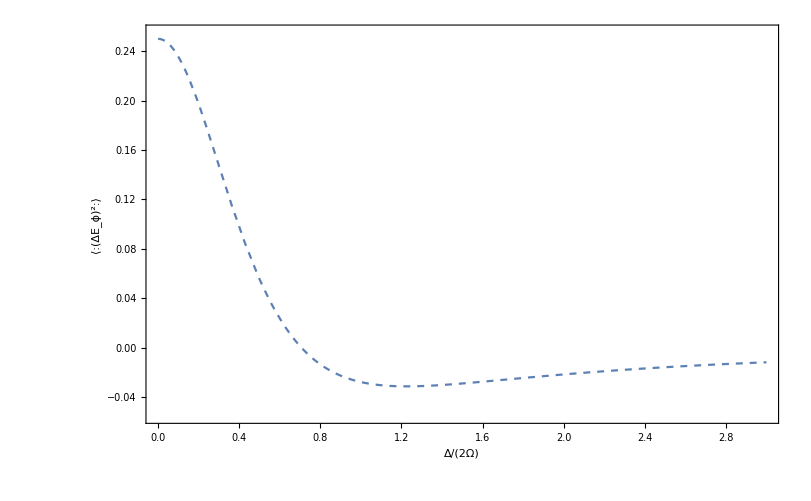

```mathematica
ω=100;
Ω=45;
g=0;
(* ϕ=-Pi/2; *)
(*q=0.7;*)
(* q=Δ/(2 Ω) *)
PzP=1;
Γs=4 Γ0+Γp+Γm;
Pz=(Γm-Γp)/(Γm+Γp);
ΩΩ=Ω √(1+q^2);
ΔΔ=ΩΩ-ω/2;
GG=g 1/(4 √(1+q^2));
G=√(GG^2+ΔΔ^2);
Cos2θ=q/(√(1+q^2));
Sin2θ=1/(√(1+q^2));
Cos2θθ=ΔΔ/G;
Sin2θθ=GG/G;
Cosθθ=√(1/2 (1+Cos2θθ));
Sinθθ=√(1-(Cos2θθ+1)/2);
Cosθ=√(1/2 (1+Cos2θ));
Sinθ=√(1-(Cos2θ+1)/2);
Cos4θ=(2 Cos2θ^2-1);
Γp=1/4 (4  Cosθ^4 Cosθθ^4+4  Sinθ^4 Sinθθ^4+ Sin2θ^2 Sin2θθ^2) ;
Γm=1/4 (4  Cosθθ^4 Sinθ^4+4  Cosθ^4 Sinθθ^4+ Sin2θ^2 Sin2θθ^2) ;Γ0=1/4 ( Cos2θθ^2 Sin2θ^2+( Cosθ^4+ Sinθ^4) Sin2θθ^2) ;

SSS=(3/4+1/4 Cos4θ+Pz Cos2θ-1/2 Sin2θ^2 Cos[2 ϕ])Cosθθ^4(Γs/(Γs^2+(2 G-n+ω)^2)+Γs/(Γs^2+(2 G+n+ω)^2))+1/2 Pz Cosθθ^4  Sin2θ^2 Sin[2 ϕ]((2 G+n+ω)/(Γs^2+(2 G+n+ω)^2)-(-2 G+n-ω)/(Γs^2+(2 G-n+ω)^2))+(3/4+1/4 Cos4θ-Pz Cos2θ-1/2 Sin2θ^2 Cos[2 ϕ])Sinθθ^4(Γs/(Γs^2+(-2 G+n+ω)^2)+Γs/(Γs^2+(2 G+n-ω)^2))-1/2 Pz Sin2θ^2 Sinθθ^4 Sin[2 ϕ]((-2 G+n+ω)/(Γs^2+(-2 G+n+ω)^2)-(2 G+n-ω)/(Γs^2+(2 G+n-ω)^2))+1/2 (Γs/((n-2 G)^2+Γs^2)+Γs/((n+2 G)^2+Γs^2)) Sin2θ^2 Sin2θθ^2(1+Cos[2 ϕ])-1/2 ((n+2 G)/((n+2 G)^2+Γs^2)-(n-2 G)/((n-2 G)^2+Γs^2))Sin[2 ϕ] Sin2θ^2 Sin2θθ^2 Pz +(PzP-Pz^2)(Sin2θ^2 Cos2θθ^2(1+Cos[2 ϕ])(Γp+Γm)/((Γp+Γm)^2+n^2)+1/2 Sin2θθ^2(Cosθ^4+Sinθ^4-1/2 Sin2θ^2 Cos[2 ϕ])((Γp+Γm)/((Γp+Γm)^2+(n+ω)^2)+(Γp+Γm)/((Γp+Γm)^2+(n-ω)^2)));

EEE=((3/4+1/4 Cos4θ+Pz Cos2θ-1/2 Sin2θ^2 Cos[2 ϕ])Cosθθ^4(2 Pi)+(3/4+1/4 Cos4θ-Pz Cos2θ-1/2 Sin2θ^2 Cos[2 ϕ])Sinθθ^4(2 Pi)+1/2 (2 Pi) Sin2θ^2 Sin2θθ^2(1+Cos[2 ϕ])+(PzP-Pz^2)(Sin2θ^2 Cos2θθ^2(1+Cos[2 ϕ])Pi+1/2 Sin2θθ^2(Cosθ^4+Sinθ^4-1/2 Sin2θ^2 Cos[2 ϕ])(2 Pi)))/(2 Pi)/4;

EEE2=(1-Cos2θ^2)/(8(1+Cos2θ^2))((1-Cos2θ^2-(1+Cos2θ^2)Cos[2 ϕ ])+(1-Cos2θ^2)^2/(1+Cos2θ^2)(1+Cos[2ϕ]));
ϕ=0;
fig0=Plot[{EEE2},{q,0,3},PlotRange->{-0.055,0.255},PlotStyle->Dashed,Frame->True,FrameTicksStyle->{Directive[FontFamily->"CMU Serif",20],Directive[FontFamily->"CMU Serif",20]},
LabelStyle->{FontFamily->"CMU Serif",24},FrameLabel->{"Δ/(2Ω)","⟨:(ΔE_ϕ)^2:⟩"}]
```

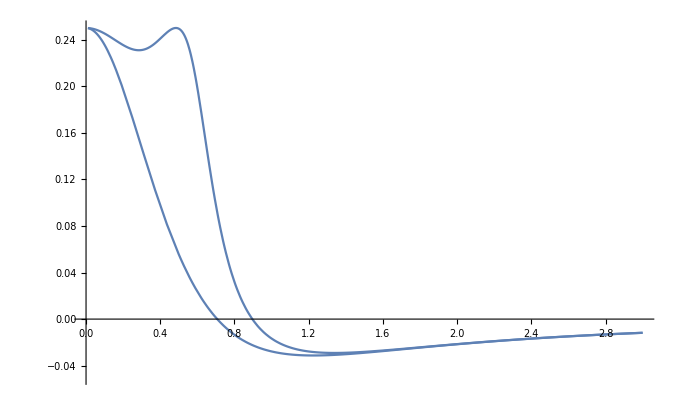

```mathematica
Show[{fig0,fig1}]
```

```mathematica
ω=100;
Ω=45;
g=16;
(* ϕ=-Pi/2; *)
q=0.7;
(*q=Δ/(2 Ω);*)
PzP=1;
Γs=4 Γ0+Γp+Γm;
Pz=(Γm-Γp)/(Γm+Γp);
ΩΩ=Ω √(1+q^2);
ΔΔ=ΩΩ-ω/2;
GG=g 1/(4 √(1+q^2));
G=√(GG^2+ΔΔ^2);
Cos2θ=q/(√(1+q^2));
Sin2θ=1/(√(1+q^2));
Cos2θθ=ΔΔ/G;
Sin2θθ=GG/G;
Cosθθ=√(1/2 (1+Cos2θθ));
Sinθθ=√(1-(Cos2θθ+1)/2);
Cosθ=√(1/2 (1+Cos2θ));
Sinθ=√(1-(Cos2θ+1)/2);
Cos4θ=(2 Cos2θ^2-1);
Γp=1/4 (4  Cosθ^4 Cosθθ^4+4  Sinθ^4 Sinθθ^4+ Sin2θ^2 Sin2θθ^2) ;
Γm=1/4 (4  Cosθθ^4 Sinθ^4+4  Cosθ^4 Sinθθ^4+ Sin2θ^2 Sin2θθ^2) ;Γ0=1/4 ( Cos2θθ^2 Sin2θ^2+( Cosθ^4+ Sinθ^4) Sin2θθ^2) ;
(*ϕ=-Pi/4;*)
SSS=(3/4+1/4 Cos4θ+Pz Cos2θ-1/2 Sin2θ^2 Cos[2 ϕ])Cosθθ^4(Γs/(Γs^2+(2 G-n+ω)^2)+Γs/(Γs^2+(2 G+n+ω)^2))+1/2 Pz Cosθθ^4  Sin2θ^2 Sin[2 ϕ]((2 G+n+ω)/(Γs^2+(2 G+n+ω)^2)-(-2 G+n-ω)/(Γs^2+(2 G-n+ω)^2))+(3/4+1/4 Cos4θ-Pz Cos2θ-1/2 Sin2θ^2 Cos[2 ϕ])Sinθθ^4(Γs/(Γs^2+(-2 G+n+ω)^2)+Γs/(Γs^2+(2 G+n-ω)^2))-1/2 Pz Sin2θ^2 Sinθθ^4 Sin[2 ϕ]((-2 G+n+ω)/(Γs^2+(-2 G+n+ω)^2)-(2 G+n-ω)/(Γs^2+(2 G+n-ω)^2))+1/2 (Γs/((n-2 G)^2+Γs^2)+Γs/((n+2 G)^2+Γs^2)) Sin2θ^2 Sin2θθ^2(1+Cos[2 ϕ])-1/2 ((n+2 G)/((n+2 G)^2+Γs^2)-(n-2 G)/((n-2 G)^2+Γs^2))Sin[2 ϕ] Sin2θ^2 Sin2θθ^2 Pz +(PzP-Pz^2)(Sin2θ^2 Cos2θθ^2(1+Cos[2 ϕ])(Γp+Γm)/((Γp+Γm)^2+n^2)+1/2 Sin2θθ^2(Cosθ^4+Sinθ^4-1/2 Sin2θ^2 Cos[2 ϕ])((Γp+Γm)/((Γp+Γm)^2+(n+ω)^2)+(Γp+Γm)/((Γp+Γm)^2+(n-ω)^2)));
ContourPlot[SSS/4,{n,-152,152},{ϕ,-Pi/2,Pi/2},PlotRange->{-1,1},Contours->1,PlotPoints->300,PlotLegends->Automatic,LabelStyle->{FontFamily->"CMU Serif",16},FrameLabel->{"ν","ϕ"},FrameTicks->{{-150,-100, -50, 0, 50,100,150},{-Pi/2,-Pi/4,0,Pi/4, Pi/2},None,None},ContourLines->False]
```

-Graphics-